```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
controlColor=Black;
```

```mathematica
(*************************)
```

```mathematica
dateMouseListControl={{"012122","Mouse22550"},{"012822","Mouse22549"},{"121621","Mouse22525"},{"121721","Mouse22599"},{"011122","Mouse22598"},{"032923","Mouse23149"},{"033023","Mouse23128"},{"033123","Mouse23149"},{"070323","Mouse23149"},{"070423","Mouse23128"},{"070723","Mouse23128"}};
```

```mathematica
(***V1 axons, eOPN3***)
```

```mathematica
dateMouseListV1axons={{"012722","Mouse22504"},{"121821","Mouse22485"},{"062723","Mouse23154"},{"062723","Mouse23182"},{"063023","Mouse23154"},{"063023","Mouse23182"}};
```

```mathematica
(***LP axons, eOPN3***)
```

```mathematica
dateMouseListLPaxons={{"050123","Mouse23133"},{"050123","Mouse23142"},{"050323","Mouse23133"},{"050323","Mouse23142"},{"051823","Mouse23198"},{"052623","Mouse23198"},{"052623","Mouse23105"},{"062923","Mouse23139"},{"070223","Mouse23139"}};
```

```mathematica
(***LM axons, eOPN3***)
```

```mathematica
dateMouseListLMaxons={{"062623","Mouse23152"},{"062823","Mouse23152"},{"062923","Mouse23190"},{"070123","Mouse23190"},{"070723","Mouse23666"},{"071223","Mouse23666"}};
```

```mathematica
pairedROIsListControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsListV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsListLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsListLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(*******************************************)
```

```mathematica
pairedPupilModIndexSummaryValsControl=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","pupilModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}],1][[All,2]];
```

```mathematica
pairedPupilModIndexSummaryValsV1axons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","pupilModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}],1][[All,2]];
```

```mathematica
pairedPupilModIndexSummaryValsLPaxons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","pupilModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}],1][[All,2]];
```

```mathematica
pairedPupilModIndexSummaryValsLMaxons=ToExpression/@Flatten[Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","pupilModPaired_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}],1][[All,2]];
```

```mathematica
(************************************)
```

```mathematica
diffsPupilControl=Table[(pairedPupilModIndexSummaryValsControl[[n,2]]-pairedPupilModIndexSummaryValsControl[[n,1]]),{n,1,Length[pairedPupilModIndexSummaryValsControl]}];
```

```mathematica
diffsPupilV1axons=Table[(pairedPupilModIndexSummaryValsV1axons[[n,2]]-pairedPupilModIndexSummaryValsV1axons[[n,1]]),{n,1,Length[pairedPupilModIndexSummaryValsV1axons]}];
```

```mathematica
diffsPupilLPaxons=Table[(pairedPupilModIndexSummaryValsLPaxons[[n,2]]-pairedPupilModIndexSummaryValsLPaxons[[n,1]]),{n,1,Length[pairedPupilModIndexSummaryValsLPaxons]}];
```

```mathematica
diffsPupilLMaxons=Table[(pairedPupilModIndexSummaryValsLMaxons[[n,2]]-pairedPupilModIndexSummaryValsLMaxons[[n,1]]),{n,1,Length[pairedPupilModIndexSummaryValsLMaxons]}];
```

```mathematica
(********************)
```

```mathematica
(***************************************************)
```

```mathematica
controlPupilModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedPupilModIndexSummaryValsControl;
```

```mathematica
allPupilModsControlDark=pairedPupilModIndexSummaryValsControl[[All,1]];
```

```mathematica
allPupilModsControlLED=pairedPupilModIndexSummaryValsControl[[All,2]];
```

```mathematica
bin=2*InterquartileRange[allPupilModsControlDark]*(Length[allPupilModsControlDark]^(-1/3))
```

0.0350628

```mathematica
minVal=Min[Join[allPupilModsControlDark,allPupilModsControlLED]];
```

```mathematica
maxVal=Max[Join[allPupilModsControlDark,allPupilModsControlLED]];
```

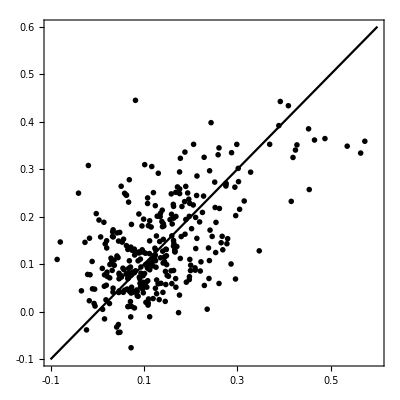

```mathematica
Show[ListPlot[pairedPupilModIndexSummaryValsControl,PlotRange->{{-0.1,0.6},{-0.1,0.6}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{controlColor,PointSize[0.01]},FrameTicks->{{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.1,0.6},PlotStyle->Black]]
```

```mathematica
pupilModIndicesControl=Table[(pairedPupilModIndexSummaryValsControl[[n,2]]-pairedPupilModIndexSummaryValsControl[[n,1]])/(pairedPupilModIndexSummaryValsControl[[n,2]]+pairedPupilModIndexSummaryValsControl[[n,1]]),{n,1,Length[pairedPupilModIndexSummaryValsControl]}];
```

```mathematica
(*******************************************)
```

```mathematica
v1AxonsPupilModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedPupilModIndexSummaryValsV1axons;
```

```mathematica
allPupilModsV1axonsDark=pairedPupilModIndexSummaryValsV1axons[[All,1]];
```

```mathematica
allPupilModsV1axonsLED=pairedPupilModIndexSummaryValsV1axons[[All,2]];
```

```mathematica
minVal=Min[Join[allPupilModsV1axonsDark,allPupilModsV1axonsLED]];
```

```mathematica
maxVal=Max[Join[allPupilModsV1axonsDark,allPupilModsV1axonsLED]];
```

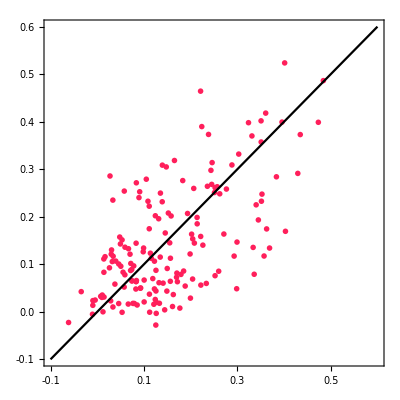

```mathematica
Show[ListPlot[pairedPupilModIndexSummaryValsV1axons,PlotRange->{{-0.1,0.6},{-0.1,0.6}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{v1Color,PointSize[0.01]},FrameTicks->{{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.1,0.6},PlotStyle->Black]]
```

```mathematica
(*******************************************)
```

```mathematica
lpAxonsPupilModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedPupilModIndexSummaryValsLPaxons;
```

```mathematica
allPupilModsLPaxonsDark=pairedPupilModIndexSummaryValsLPaxons[[All,1]];
```

```mathematica
allPupilModsLPaxonsLED=pairedPupilModIndexSummaryValsLPaxons[[All,2]];
```

```mathematica
minVal=Min[Join[allPupilModsLPaxonsDark,allPupilModsLPaxonsLED]];
```

```mathematica
maxVal=Max[Join[allPupilModsLPaxonsDark,allPupilModsLPaxonsLED]];
```

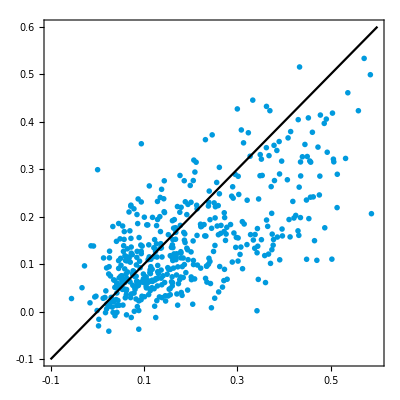

```mathematica
Show[ListPlot[pairedPupilModIndexSummaryValsLPaxons,PlotRange->{{-0.1,0.6},{-0.1,0.6}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lpColor,PointSize[0.01]},FrameTicks->{{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.1,0.6},PlotStyle->Black]]
```

```mathematica
(*******************************************)
```

```mathematica
lmAxonsPupilModPairsPlotPts=Partition[Riffle[{0.4,0.6} ,#],2]&/@pairedPupilModIndexSummaryValsLMaxons;
```

```mathematica
allPupilModsLMaxonsDark=pairedPupilModIndexSummaryValsLMaxons[[All,1]];
```

```mathematica
allPupilModsLMaxonsLED=pairedPupilModIndexSummaryValsLMaxons[[All,2]];
```

```mathematica
minVal=Min[Join[allPupilModsLMaxonsDark,allPupilModsLMaxonsLED]];
```

```mathematica
maxVal=Max[Join[allPupilModsLMaxonsDark,allPupilModsLMaxonsLED]];
```

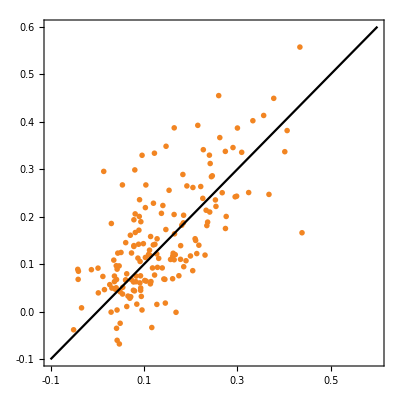

```mathematica
Show[ListPlot[pairedPupilModIndexSummaryValsLMaxons,PlotRange->{{-0.1,0.6},{-0.1,0.6}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lmColor,PointSize[0.01]},FrameTicks->{{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.1,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,-0.1,0.6},PlotStyle->Black]]
```

```mathematica
(***********************************************************)
```

```mathematica
(************)
```

```mathematica
bin=2*InterquartileRange[diffsPupilControl]*(Length[diffsPupilControl]^(-1/3))
```

0.0328515

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsPupilControl},{-0.7,0.7,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{controlColor}),PerformanceGoal->"Speed",PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
h2=Histogram[{diffsPupilControl},{-0.7,0.7,bin},hfn,ChartStyle->{{controlColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

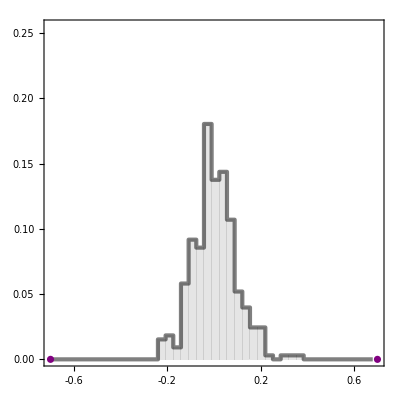

```mathematica
histModIndexControl=Show[hline,h2,ListPlot[{{-0.7,0},{0.7,0}},PlotStyle->Purple],PlotRange->{{-0.7,0.7},{0,0.255}},FrameTicks->{{LinTicks[0,0.255,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsPupilV1axons]*(Length[diffsPupilV1axons]^(-1/3))
```

0.052342

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsPupilV1axons},{-0.7,0.7,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{v1Color}),PerformanceGoal->"Speed",PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
h2=Histogram[{diffsPupilV1axons},{-0.7,0.7,bin},hfn,ChartStyle->{{v1Color},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

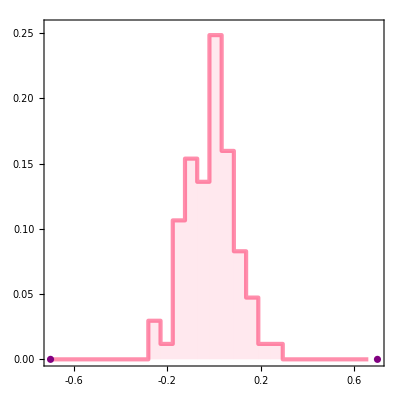

```mathematica
histModIndexV1axons=Show[hline,h2,ListPlot[{{-0.7,0},{0.7,0}},PlotStyle->Purple],PlotRange->{{-0.7,0.7},{0,0.255}},FrameTicks->{{LinTicks[0,0.255,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsPupilLPaxons]*(Length[diffsPupilLPaxons]^(-1/3))
```

0.031856

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsPupilLPaxons},{-0.7,0.7,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lpColor}),PerformanceGoal->"Speed",PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
h2=Histogram[{diffsPupilLPaxons},{-0.7,0.7,bin},hfn,ChartStyle->{{lpColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

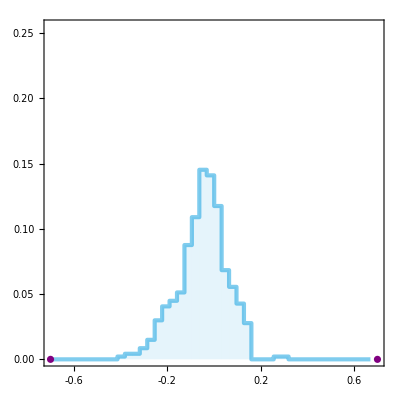

```mathematica
histModIndexLPaxons=Show[hline,h2,ListPlot[{{-0.7,0},{0.7,0}},PlotStyle->Purple],PlotRange->{{-0.7,0.7},{0,0.255}},FrameTicks->{{LinTicks[0,0.255,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsPupilLMaxons]*(Length[diffsPupilLMaxons]^(-1/3))
```

0.0422579

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsPupilLMaxons},{-0.7,0.7,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lmColor}),PerformanceGoal->"Speed",PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
h2=Histogram[{diffsPupilLMaxons},{-0.7,0.7,bin},hfn,ChartStyle->{{lmColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.7,0.7},{0,0.255}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

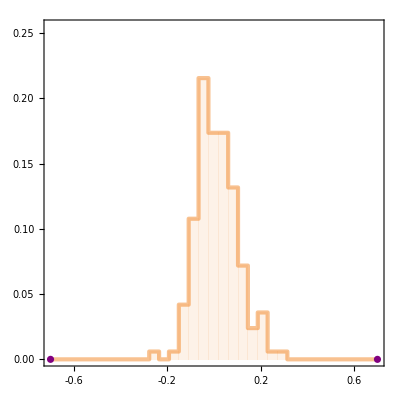

```mathematica
histModIndexLMaxons=Show[hline,h2,ListPlot[{{-0.7,0},{0.7,0}},PlotStyle->Purple],PlotRange->{{-0.7,0.7},{0,0.255}},FrameTicks->{{LinTicks[0,0.255,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
controlCharts=Show[BoxWhiskerChart[diffsPupilControl,{{"Whiskers", Directive[Darker@controlColor,Thick]}, {"Fences", Directive[Darker@controlColor,Thick]},{"MedianMarker", Directive[Darker@controlColor,Thickness[0.009]]}},PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[controlColor,Opacity[0.3]],Frame->False],DistributionChart[diffsPupilControl,PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],controlColor],Frame->False],FrameTicks->{{LinTicks[-0.4,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[diffsPupilV1axons,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[diffsPupilV1axons,PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-0.4,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[diffsPupilLPaxons,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[diffsPupilLPaxons,PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-0.4,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[diffsPupilLMaxons,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[diffsPupilLMaxons,PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-0.4,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[diffsPupilControl,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-0.4,0.4}},ChartStyle->Transparent,Frame->False],DistributionChart[diffsPupilControl,PlotRange->{All,{-0.4,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-0.4,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

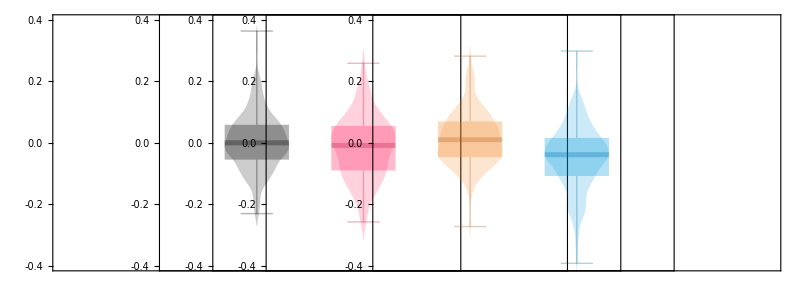

```mathematica
GraphicsRow[{controlCharts,v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```